```mathematica
(* ΔΙΠΛΟ ΟΡΘΟΓΩΝΙΟ ΦΡΕΑΡ ΔΥΝΑΜΙΚΟΥ *)
```

```mathematica
Clear["Global`*"]
```

```mathematica
(* ΟΡΙΣΜΟΣ ΣΤΑΘΕΡΩΝ, 1 ΓΙΑ ΑΤΟΜΙΚΑ ΚΑΙ 2 ΓΙΑ ΠΥΡΗΝΙΚΑ ΣΥΣΤΗΜΑΤΑ *)
```

```mathematica
ic=1; 
Which[ ic==1, {c=26.247 , ctime=6.586*10^(-16)},
           ic==2, {c=0.0482, ctime=6.586*10^(-21)}     ];
```

```mathematica
(* ΟΡΙΣΜΟΣ ΠΑΡΑΜΕΤΡΩΝ ΤΟΥ ΔΥΝΑΜΙΚΟΥ *)
```

```mathematica
{v0=300, L0=0.2, v1=200, L1=0.1};
```

```mathematica
(* ΟΡΙΣΜΟΣ ΚΑΙ PLOT ΤΟΥ ΔΥΝΑΜΙΚΟΥ *)
```

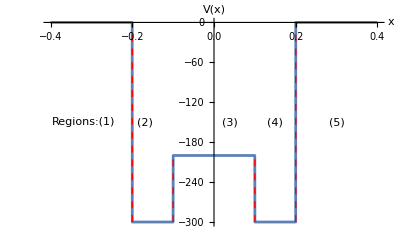

```mathematica
v[x_]:=Which[ L1< Abs[x]≤L0,  -v0 ,
                            Abs[x] >L0, 0 ,
                             Abs[x]<L1, -v1         ]; 
lineStyle={Thick,Red,Dashed};
line1=Line[{{-0.2,-300},{-0.2,0}}];
line2=Line[{{0.2,-300},{0.2,0}}];
line3=Line[{{0.1,-300},{0.1,-200}}];
line4=Line[{{-0.1,-300},{-0.1,-200}}];
 Plot[ v[x], {x, -2*L0, 2*L0}, PlotStyle ->AbsoluteThickness[2],
AxesStyle -> AbsoluteThickness[1], AxesLabel->{"x","V(x)"},
Epilog->{Text[StyleForm["Regions:(1)"], {-0.32, -150}] ,
                  Text[StyleForm[" (2)"], {-0.17, -150}],
                  Text[StyleForm[" (3)"], {0.04, -150}],
                  Text[StyleForm[" (4)"], {0.15, -150}],
                  Text[StyleForm[" (5)"], {0.3, -150}]  ,Directive[lineStyle],line1,line2,line3,line4   }   ]
```

```mathematica
(* ΟΡΙΖΟΥΜΕ ΤΟΥΣ ΚΥΜΑΤΑΡΙΘΜΟΥΣ ΩΣ ΣΥΝΑΡΤΗΣΗ ΤΗΣ ΕΝΕΡΓΕΙΑΣ ΚΑΙ ΤΩΝ ΙΔΙΟΤΙΜΩΝ ΓΙΑ ΤΙΣ ΑΡΤΙΕΣ ΚΑΙ ΤΙΣ ΠΕΡΙΤΤΕΣ ΚΑΤΑΣΤΑΣΕΙΣ *)
```

```mathematica
(* ΟΡΙΣΜΟΣ ΚΥΜΑΤΑΡΙΘΜΩΝ γ, κ0, κ1 ΩΣ ΣΥΝΑΡΤΗΣΕΙΣ ΤΗΣ ΕΝΕΡΓΕΙΑΣ ΑΠΟ ΤΗΝ ΣΧΕΣΗ 1.80 *)
```

```mathematica
g[e_]:=Sqrt[-c*e]; 
k0[e_]:=Sqrt[c*(e+v0)]; 
k1[e_]:=Sqrt[Abs[c*(e+v1)]];
```

```mathematica
(* ΟΡΙΣΜΟΣ ΕΞΙΣΩΣΕΩΝ ΠΕΡΙΤΤΩΝ ΚΑΤΑΣΤΑΣΕΩΝ (1.84 & 1.87) ΩΣ ΣΥΝΑΡΤΗΣΕΙΣ ΤΗΣ ΕΝΕΡΓΕΙΑΣ ΚΑΙ ΤΗΣ ΦΑΣΗΣ *)
```

```mathematica
eqEvenOdd[e_,fi_]:=g[e]*Cos[k0[e]*L0+fi]-k0[e]*Sin[k0[e]*L0+fi];
eq2Even[e_,fi_]:=k0[e]*Sin[k0[e]*L1+fi]*Cosh[k1[e]*L1] + 
                               k1[e]*Cos[k0[e]*L1+fi]*Sinh[k1[e]*L1];  

eq2Odd[e_,fi_]:=k0[e]*Sin[k0[e]*L1+fi]*Sinh[k1[e]*L1] +
                               k1[e]*Cos[k0[e]*L1+fi]*Cosh[k1[e]*L1];
```

```mathematica
(* ΘΑ ΘΕΩΡΗΣΟΥΜΕ ΤΗΝ ΠΕΡΙΠΤΩΣΗ ΟΠΟΥ|E|>V1 *)
```

```mathematica
(* ΕΠΙΛΥΣΗ ΤΟΥ ΣΥΣΤΗΜΑΤΟΣ ΕΞΙΣΩΣΕΩΝ eqEvenOdd[e,fi]=0 ΚΑΙ eq2Odd[e,fi]=0 ΓΙΑ ΠΕΡΙΤΤΕΣ ΚΑΤΑΣΤΑΣΕΙΣ ΜΕ ΤΗΝ ΕΝΤΟΛΗ FindRoot *)
```

```mathematica
nOdd=0; (* ΑΡΙΘΜΟΣ ΠΕΡΙΤΤΩΝ ΚΑΤΑΣΤΑΣΕΩΝ *)
eOdd=fiOdd=testOdd=Table[Null,{20}];
(* ΕΠΙΛΥΣΗ ΤΟΥ ΣΥΣΤΗΜΑΤΟΣ ΕΞΙΣΩΣΕΩΝ eqEvenOdd[e,fi]=0 ΚΑΙ eqEven[e,fi]=0 ΓΙΑ ΑΡΤΙΕΣ ΚΑΤΑΣΤΑΣΕΙΣ ΜΕ ΤΗΝ ΕΝΤΟΛΗ FindRoot *)
nEven=0;(* ΑΡΙΘΜΟΣ ΑΡΤΙΩΝ ΚΑΤΑΣΤΑΣΕΩΝ *)
eEven=fiEven=testEven=Table[Null,{20}];
(* Do loop ΜΕΧΡΙ E >-v1 *)
(* ΤΑ ΔΙΑΣΤΗΜΑΤΑ Εmin & Emax ΤΑ ΠΑΙΡΝΟΥΜΕ ΑΠΟ ΤΗΝ ΑΝΤΙΣΤΟΙΧΗ ΣΧΕΣΗ ΓΙΑ ΤΟ ΟΡΘΟΓΩΝΙΟ ΦΡΕΑΡ ΔΥΝΑΜΙΚΟΥ, ΣΧΕΣΗ 1.71  *)
Do[ {  Emin=-v0+ (2*n-1)^2*Pi^2/(4*c*L0^2),
Emax=-v0+ (2*n)^2*Pi^2/(4*c*L0^2),
If[Emin >-v1, Break[] ],
(* ΕΠΙΛΥΣΗ ΜΕ FindRoot *)
enfi=FindRoot[{eqEvenOdd[e,fi]==0, eq2Odd[e,fi]==0,eq2Even[e,fi]==0},
                         {e,Emin,Emax}, {fi,0,Pi/2}  ],
(* ΔΥΟ ΡΙΖΕΣ: eSave & fiSave *)
eSave=e/.enfi, fiSave=fi/.enfi,
(* ΕΥΡΕΣΗ ΑΘΡΟΙΣΜΑΤΟΣ ΤΩΝ ΜΕΤΡΩΝ ΤΩΝ eqEvenOdd & eq2Even &eq2Odd*)
test=Abs[eqEvenOdd[eSave,fiSave ] ]+ Abs[eq2Odd[eSave,fiSave  ]]+Abs[eq2Even[eSave,fiSave]],
Print["e[",n,"]=", eSave,"  fi[",n,"]=",fiSave," test=",test],
(* ΕΛΕΓΧΟΣ ΑΚΡΙΒΕΙΑΣ ΤΗΣ ΡΙΖΑΣ *)
(* ΣΕ ΠΕΡΙΠΤΩΣΗ ΠΟΥ ΕΙΝΑΙ ΟΚ, ΥΠΟΛΟΓΙΖΟΥΜΕ ΤΗΝ ΕΠΟΜΕΝΗ *)
If[test <0.00001, nOdd=nOdd+1 ,nEven=nEven+1;
eEven[[nEven]]=eSave; fiEven[[nEven]]=fiSave;testEven[[nEven]]=test,
eOdd[[nOdd]]=eSave; fiOdd[[nOdd]]=fiSave;testOdd[[nOdd]]=test ],
Clear[Emin,Emax,enfi,eSave, fiSave]
  }, {n,1,10}]
(*  *)
Print["The eingevalues of the odd states for |E|>V1"]
Do[Print["Odd State: e[",n,"]=", eOdd[[n]]," fi[",n,"]=",fiOdd[[n]]," test=",testOdd[[n]],"Even State:e[",n,"]=",eEven[[n]],"fi[",n,"]=",fiEven[[n]] ], {n,1,nOdd}]
```

ReplaceAll::reps: {NFindRoot[{5.12318 √Times[«2»] Cos[Plus[«2»]]-5.12318 √Plus[«2»] Sin[Plus[«2»]]==0,5.12318 √Abs[«1»] Cos[Plus[«2»]] Cosh[Times[«2»]]+5.12318 √Plus[«2»] Sin[Plus[«2»]] Sinh[Times[«2»]]==0,5.12318 √Plus[«2»] Cosh[Times[«2»]] Sin[Plus[«2»]]+5.12318 √Abs[«1»] Cos[Plus[«2»]] Sinh[Times[«2»]]==0},{e,-«18»,-«18»},{fi,0,π/2}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

e[1]=e/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-297.65,-290.599},{fi,0,π/2}]  fi[1]=fi/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-297.65,-290.599},{fi,0,π/2}] test=Abs[5.12318 Cos[1.02464 √(300+(e/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-297.65,-290.599},{fi,0,π/2}]))+(fi/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-297.65,-290.599},{fi,0,π/2}])] √(-(e/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-297.65,-290.599},{fi,0,π/2}]))-5.12318 √(300+(e/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-297.65,-290.599},{fi,0,π/2}])) Sin[1.02464 √(300+(e/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-297.65,-290.599},{fi,0,π/2}]))+(fi/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-297.65,-290.599},{fi,0,π/2}])]]+Abs[5.12318 Cosh[0.512318 √Abs[200+(e/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-297.65,-290.599},{fi,0,π/2}])]] √(300+(e/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-297.65,-290.599},{fi,0,π/2}])) Sin[0.512318 √(300+(e/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-297.65,-290.599},{fi,0,π/2}]))+(fi/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-297.65,-290.599},{fi,0,π/2}])]+5.12318 √Abs[200+(e/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-297.65,-290.599},{fi,0,π/2}])] Cos[0.512318 √(300+(e/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-297.65,-290.599},{fi,0,π/2}]))+(fi/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-297.65,-290.599},{fi,0,π/2}])] Sinh[0.512318 √Abs[200+(e/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-297.65,-290.599},{fi,0,π/2}])]]]+Abs[5.12318 √Abs[200+(e/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-297.65,-290.599},{fi,0,π/2}])] Cos[0.512318 √(300+(e/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-297.65,-290.599},{fi,0,π/2}]))+(fi/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-297.65,-290.599},{fi,0,π/2}])] Cosh[0.512318 √Abs[200+(e/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-297.65,-290.599},{fi,0,π/2}])]]+5.12318 √(300+(e/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-297.65,-290.599},{fi,0,π/2}])) Sin[0.512318 √(300+(e/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-297.65,-290.599},{fi,0,π/2}]))+(fi/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-297.65,-290.599},{fi,0,π/2}])] Sinh[0.512318 √Abs[200+(e/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-297.65,-290.599},{fi,0,π/2}])]]]

ReplaceAll::reps: {NFindRoot[{5.12318 √Times[«2»] Cos[Plus[«2»]]-5.12318 √Plus[«2»] Sin[Plus[«2»]]==0,5.12318 √Abs[«1»] Cos[Plus[«2»]] Cosh[Times[«2»]]+5.12318 √Plus[«2»] Sin[Plus[«2»]] Sinh[Times[«2»]]==0,5.12318 √Plus[«2»] Cosh[Times[«2»]] Sin[Plus[«2»]]+5.12318 √Abs[«1»] Cos[Plus[«2»]] Sinh[Times[«2»]]==0},{e,-«18»,-«19»},{fi,0,π/2}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

e[2]=e/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-278.848,-262.397},{fi,0,π/2}]  fi[2]=fi/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-278.848,-262.397},{fi,0,π/2}] test=Abs[5.12318 Cos[1.02464 √(300+(e/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-278.848,-262.397},{fi,0,π/2}]))+(fi/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-278.848,-262.397},{fi,0,π/2}])] √(-(e/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-278.848,-262.397},{fi,0,π/2}]))-5.12318 √(300+(e/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-278.848,-262.397},{fi,0,π/2}])) Sin[1.02464 √(300+(e/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-278.848,-262.397},{fi,0,π/2}]))+(fi/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-278.848,-262.397},{fi,0,π/2}])]]+Abs[5.12318 Cosh[0.512318 √Abs[200+(e/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-278.848,-262.397},{fi,0,π/2}])]] √(300+(e/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-278.848,-262.397},{fi,0,π/2}])) Sin[0.512318 √(300+(e/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-278.848,-262.397},{fi,0,π/2}]))+(fi/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-278.848,-262.397},{fi,0,π/2}])]+5.12318 √Abs[200+(e/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-278.848,-262.397},{fi,0,π/2}])] Cos[0.512318 √(300+(e/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-278.848,-262.397},{fi,0,π/2}]))+(fi/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-278.848,-262.397},{fi,0,π/2}])] Sinh[0.512318 √Abs[200+(e/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-278.848,-262.397},{fi,0,π/2}])]]]+Abs[5.12318 √Abs[200+(e/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-278.848,-262.397},{fi,0,π/2}])] Cos[0.512318 √(300+(e/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-278.848,-262.397},{fi,0,π/2}]))+(fi/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-278.848,-262.397},{fi,0,π/2}])] Cosh[0.512318 √Abs[200+(e/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-278.848,-262.397},{fi,0,π/2}])]]+5.12318 √(300+(e/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-278.848,-262.397},{fi,0,π/2}])) Sin[0.512318 √(300+(e/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-278.848,-262.397},{fi,0,π/2}]))+(fi/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-278.848,-262.397},{fi,0,π/2}])] Sinh[0.512318 √Abs[200+(e/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-278.848,-262.397},{fi,0,π/2}])]]]

e[3]=e/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-241.246,-215.394},{fi,0,π/2}]  fi[3]=fi/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-241.246,-215.394},{fi,0,π/2}] test=Abs[5.12318 Cos[1.02464 √(300+(e/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-241.246,-215.394},{fi,0,π/2}]))+(fi/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-241.246,-215.394},{fi,0,π/2}])] √(-(e/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-241.246,-215.394},{fi,0,π/2}]))-5.12318 √(300+(e/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-241.246,-215.394},{fi,0,π/2}])) Sin[1.02464 √(300+(e/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-241.246,-215.394},{fi,0,π/2}]))+(fi/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-241.246,-215.394},{fi,0,π/2}])]]+Abs[5.12318 Cosh[0.512318 √Abs[200+(e/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-241.246,-215.394},{fi,0,π/2}])]] √(300+(e/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-241.246,-215.394},{fi,0,π/2}])) Sin[0.512318 √(300+(e/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-241.246,-215.394},{fi,0,π/2}]))+(fi/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-241.246,-215.394},{fi,0,π/2}])]+5.12318 √Abs[200+(e/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-241.246,-215.394},{fi,0,π/2}])] Cos[0.512318 √(300+(e/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-241.246,-215.394},{fi,0,π/2}]))+(fi/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-241.246,-215.394},{fi,0,π/2}])] Sinh[0.512318 √Abs[200+(e/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-241.246,-215.394},{fi,0,π/2}])]]]+Abs[5.12318 √Abs[200+(e/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-241.246,-215.394},{fi,0,π/2}])] Cos[0.512318 √(300+(e/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-241.246,-215.394},{fi,0,π/2}]))+(fi/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-241.246,-215.394},{fi,0,π/2}])] Cosh[0.512318 √Abs[200+(e/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-241.246,-215.394},{fi,0,π/2}])]]+5.12318 √(300+(e/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-241.246,-215.394},{fi,0,π/2}])) Sin[0.512318 √(300+(e/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-241.246,-215.394},{fi,0,π/2}]))+(fi/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-241.246,-215.394},{fi,0,π/2}])] Sinh[0.512318 √Abs[200+(e/.NFindRoot[{5.12318 √-e Cos[1.02464 √(300+e)+fi]-5.12318 √(300+e) Sin[1.02464 √(300+e)+fi]==0,5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Cosh[0.512318 √Abs[200+e]]+5.12318 √(300+e) Sin[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0,5.12318 √(300+e) Cosh[0.512318 √Abs[200+e]] Sin[0.512318 √(300+e)+fi]+5.12318 √Abs[200+e] Cos[0.512318 √(300+e)+fi] Sinh[0.512318 √Abs[200+e]]==0},{e,-241.246,-215.394},{fi,0,π/2}])]]]

The eingevalues of the odd states for |E|>V1

```mathematica
(* ΕΥΡΕΣΗ ΜΟΝΑΔΙΚΩΝ ΡΙΖΩΝ *)
```

```mathematica
iod=0;eOdd[[nOdd+1]]=0;

(* ΕΛΕΓΧΟΣ ΓΙΑ ΚΑΘΕ ΡΙΖΑ ΠΟΥ ΒΡΗΚΑΜΕ ΑΝ ΕΙΝΑΙ Η ΙΔΙΑ ΜΕ ΤΗΝ ΠΡΟΗΓΟΥΜΕΝΗ *)
Do[{ If[ Abs[eOdd[[i]]-eOdd[[i+1]]]<0.0001 ,{ }   ,
iod=iod+1;
eOdd[[iod]]=eOdd[[i]];fiOdd[[iod]]=fiOdd[[i]] ;
Print["Odd State Energy[",iod,"]=",eOdd[[iod]] ];
  ] 
}, {i,1,nOdd+1}];
(* ΕΥΡΕΣΗ ΜΟΝΑΔΙΚΩΝ ΡΙΖΩΝ *)

iev=0;eEven[[nEven+1]]=0.;
(* ΕΛΕΓΧΟΣ ΓΙΑ ΚΑΘΕ ΡΙΖΑ ΠΟΥ ΒΡΗΚΑΜΕ ΑΝ ΕΙΝΑΙ Η ΙΔΙΑ ΜΕ ΤΗΝ ΠΡΟΗΓΟΥΜΕΝΗ *)
Do[{ If[ Abs[eEven[[i]]-eEven[[i+1]] ]<0.0001 ,{ }   ,
 iev=iev+1 ;
eEven[[iev]]=eEven[[i]];fiEven[[iev]]=fiEven[[i]];
Print["Even State Energy[",iev,"]=",eEven[[iev]]] ;
   ]
}, {i,1,nEven+1}]
```

ReplaceAll::argx: e«2»NFindRoot[{5.12318 √Times[«2»] Cos[Plus[«2»]]-5.12318 √Plus[«2»] Sin[Plus[«2»]]==0,5.12318 √Abs[«1»] Cos[Plus[«2»]] Cosh[Times[«2»]]+5.12318 √Plus[«2»] Sin[Plus[«2»]] Sinh[Times[«2»]]==0,5.12318 √Plus[«2»] Cosh[Times[«2»]] Sin[Plus[«2»]]+5.12318 √Abs[«1»] Cos[Plus[«2»]] Sinh[Times[«2»]]==0},{e,«1»,-«18»},{fi,0,π/2}] called with 20 arguments; 1 argument is expected.

```mathematica
(* ΕΥΡΕΣΗ ΚΥΜΑΤΟΣΥΝΑΡΤΗΣΕΩΝ ΓΙΑ ΠΕΡΙΤΤΕΣ ΚΑΙ ΑΡΤΙΕΣ ΚΑΤΑΣΤΑΣΕΙΣ *)
```

```mathematica
(* ΟΡΙΣΜΟΣ ΣΤΑΘΕΡΩΝ Α2, Α3, Β3 *)
a2[e_,fi_]:= Exp[-g[e]*L0]/Cos[k0[e]*L0+fi] ;
a3[e_,fi_]:=   a2[e,fi]*Cos[k0[e]*L1+fi]/Cosh[k1[e]*L1];
b3[e_,fi_]:=-a2[e,fi]*Cos[k0[e]*L1+fi]/Sinh[k1[e]*L1];
```

```mathematica
(* ΟΡΙΣΜΟΣ ΜΗ ΚΑΝΟΝΙΚΟΠΟΙΗΜΕΝΗΣ ΚΥΜΑΤΟΣΥΝΑΡΤΗΣΗΣ *)
wf1odd[e_,fi_,x_]:= Which[ 
           x≤-L0,  Exp[g[e]*x ]  ,
             x>L0,  -Exp[-g[e]*x ] ,
 -L0<x≤-L1, a2[e,fi]*Cos[-k0[e]*x+fi] ,
   -L1<x≤L1, b3[e,fi]*Sinh[k1[e]*x],
     L1<x≤L0, -a2[e,fi]*Cos[k0[e]*x+fi]          ];
wf1even[e_,fi_,x_]:= Which[ 
           x≤-L0,  Exp[g[e]*x ]  ,
             x>L0,  Exp[-g[e]*x ] ,
 -L0<x≤-L1, a2[e,fi]*Cos[-k0[e]*x+fi] ,
   -L1<x≤L1, a3[e,fi]*Cosh[k1[e]*x],
     L1<x≤L0, a2[e,fi]*Cos[k0[e]*x+fi]          ];
(* ΟΡΙΣΜΟΣ ΠΑΡΑΓΟΝΤΑ ΚΑΝΟΝΟΙΚΟΠΟΙΗΣΗΣ *)
normodd[e_,fi_]:=Sqrt[2* NIntegrate[wf1odd[e,fi,x]^2, {x,-5*L0, 0}
 ,MaxRecursion->10   ]  ] ;
normeven[e_,fi_]:=Sqrt[2* NIntegrate[wf1even[e,fi,x]^2, {x,-5*L0, 0}
 ,MaxRecursion->10   ]  ] ;
(* ΟΡΙΣΜΟΣ ΚΑΝΟΝΙΚΟΠΟΙΗΜΕΝΗΣ ΚΥΜΑΤΟΣΥΝΑΡΤΗΣΗΣ *)
wfodd[e_,fi_,x_]:= wf1odd[e,fi,x]/normodd[e,fi] ;
wfeven[e_,fi_,x_]:= wf1even[e,fi,x]/normeven[e,fi] ;
```

```mathematica
(* ΓΡΑΦΙΚΟΣ ΥΠΟΛΟΓΙΣΜΟΣ ΚΥΜΑΤΟΣΥΝΑΡΤΗΣΕΩΝ ΚΑΙ ΠΥΚΝΟΤΗΤΩΝ ΠΙΘΑΝΟΤΗΤΑΣ *)
```

```mathematica
Do[  {  e=eOdd[[i]], fi=fiOdd[[i]],
figWF=Plot[Evaluate[wfodd[e,fi,x] ], {x, -2*L0, 2*L0}, 
DisplayFunction->Identity,
PlotRange->All, AxesLabel->{"x " ,"  WFodd(x)" }],
figDEN=Plot[Evaluate[wfodd[e,fi,x]^2 ], {x, -2*L0, 2*L0}, 
DisplayFunction-> Identity,
PlotRange->All, AxesLabel->{"x " ,"     DENodd(x)" }],
Print[ " odd bound state energy[",i,"]=",eOdd[[i]]   ] 
}, {i,1,iod}  ];
Do[  {  e=eEven[[i]], fi=fiEven[[i]],
figWF=Plot[Evaluate[wfeven[e,fi,x] ], {x, -2*L0, 2*L0}, 
DisplayFunction->Identity,
PlotRange->All, AxesLabel->{"x " ,"  WFeven(x)" }],
figDEN=Plot[Evaluate[wfeven[e,fi,x]^2 ], {x, -2*L0, 2*L0}, 
DisplayFunction-> Identity,
PlotRange->All, AxesLabel->{"x " ,"     DENeven(x)" }],
Print[ " even bound state energy[",i,"]=",eEven[[i]]   ] 
}, {i,1,iev}  ];
```

```mathematica
(* PLOT ΚΥΜΑΤΟΣΥΝΑΡΤΗΣΕΩΝ ΜΕ ΤΗΝ ΒΟΗΘΕΙΑ ΔΗΜΙΟΥΡΓΙΑΣ ΠΙΝΑΚΑ ΣΤΟΙΧΕΙΩΝ iod ΟΠΟΥ ΕΙΝΑΙ ΤΟ ΠΛΗΘΟΣ ΤΩΝ ΠΕΡΙΤΤΩΝ ΚΑΙ ΑΡΤΙΩΝ ΚΥΜΑΤΟΣΥΝΑΡΤΗΣΕΩΝ ΠΟΥ ΥΠΟΛΟΓΙΣΤΙΚΑΝ *)
```

```mathematica
figWF=Plot[Evaluate[Table[wfodd[eOdd[[i]],fiOdd[[i]],x] ,{i,1,iod}]], {x, -0.4, 0.4}, 
 AxesLabel->{"x " ,"  WFodd(x)" }]
figW=Plot[Evaluate[Table[wfeven[eEven[[i]],fiEven[[i]],x] ,{i,1,iod}]], {x, -0.4, 0.4}, 
 AxesLabel->{"x " ,"  WFodd(x)" }]
```

-Graphics-

-Graphics-

```mathematica
(* PLOT ΠΥΚΝΟΤΗΤΩΝ ΠΙΘΑΝΟΤΗΤΑΣ ΜΕ ΤΗΝ ΒΟΗΘΕΙΑ ΔΗΜΙΟΥΡΓΙΑΣ ΠΙΝΑΚΑ ΣΤΟΙΧΕΙΩΝ iod (iev) ΟΠΟΥ ΕΙΝΑΙ ΤΟ ΠΛΗΘΟΣ ΤΩΝ ΠΕΡΙΤΤΩΝ (ΚΑΙ ΑΡΤΙΩΝ) ΚΥΜΑΤΟΣΥΝΑΡΤΗΣΕΩΝ ΠΟΥ ΥΠΟΛΟΓΙΣΤΙΚΑΝ *)
```

```mathematica
figDEN=Plot[Evaluate[Table[wfodd[eOdd[[i]],fiOdd[[i]],x]^2 ,{i,1,iod}]], {x, -0.4, 0.4}, 
 AxesLabel->{"x " ,"     DENodd(x)" }]
figDEN=Plot[Evaluate[Table[wfeven[eEven[[i]],fiEven[[i]],x]^2 ,{i,1,iev}]], {x, -0.4, 0.4}, 
 AxesLabel->{"x " ,"     DENeven(x)" }]
```

-Graphics-

-Graphics-